```mathematica
Needs["IGraphM`"]
```

```mathematica
configurationModel[degrees_]:=With[{stubs=Catenate@MapIndexed[ConstantArray[First[#2],#1]&,degrees]},Graph[Range@Length[degrees],UndirectedEdge@@@Partition[RandomSample[stubs],2]]]
```

```mathematica
configurationModel[{2,2}]
```

-Graphics-

```mathematica
configurationModel[{1,1,1}]
```

```mathematica
SimpleGraphQ[%]
```

False

```mathematica
k=10000;
r=N[#[True]/(#[True]+#[False])]&@Counts[SimpleGraphQ/@Table[
configurationModel[VertexDegree[RandomGraph[BernoulliGraphDistribution[5, 0.5]]]]
,{k}
]];

r
```

0.2838

```mathematica
k=10000;
d=Table[N[Lookup[#,True,0]/(Lookup[#,True,0]+Lookup[#,False,0])]&@Counts[SimpleGraphQ/@Table[
configurationModel[Prepend[ConstantArray[1,m],m]]
,{k}
]],{m,1,15}]
```

{1.,0.6708,0.4011,0.2299,0.1246,0.066,0.0374,0.0179,0.0128,0.0053,0.003,0.0009,0.0011,0.0008,0.0004}

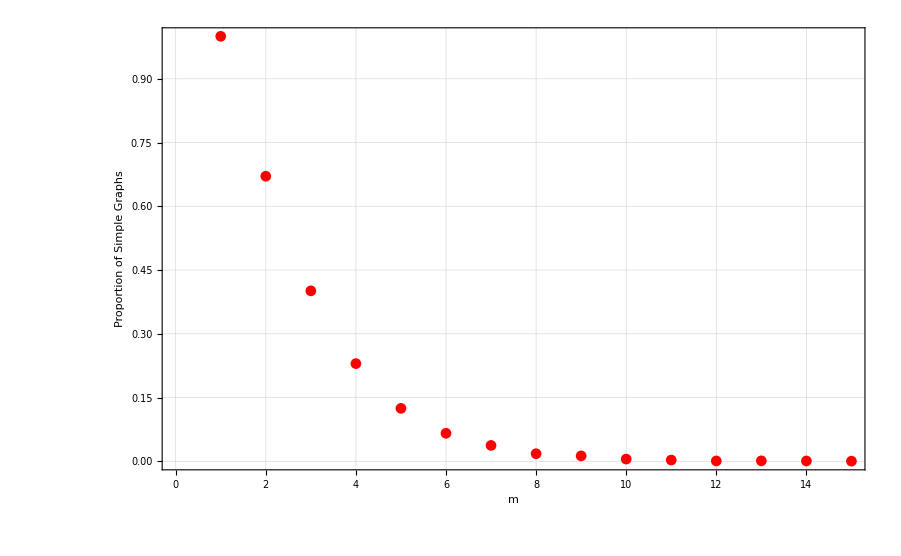

```mathematica
ListPlot[d,Frame->True,FrameLabel->{"m","Proportion of Simple Graphs"},PlotStyle->{Red,Thick},GridLines->Automatic,PlotMarkers->Automatic]
```

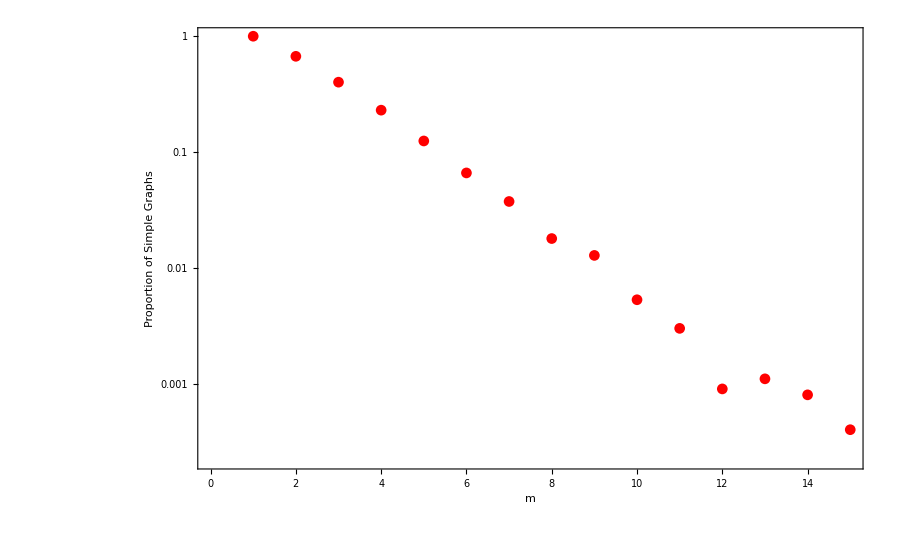

```mathematica
ListLogPlot[d,Frame->True,FrameLabel->{"m","Proportion of Simple Graphs"},PlotStyle->{Red,Thick},GridLines->Automatic,PlotMarkers->Automatic]
```

```mathematica
m=7
Prepend[ConstantArray[1,m],m]
```

7

{7,1,1,1,1,1,1,1}

```mathematica
d=Table[{1-m,N[Lookup[#,True,0]/(Lookup[#,True,0]+Lookup[#,False,0])]}&@Counts[SimpleGraphQ/@Table[
configurationModel[VertexDegree[RandomGraph[BernoulliGraphDistribution[5, 1-m]]]]
,{k}
]],{m,0,1, 0.1}]
```

{{1.,0.0108},{0.9,0.0218},{0.8,0.0491},{0.7,0.0946},{0.6,0.1685},{0.5,0.2902},{0.4,0.4291},{0.3,0.5905},{0.2,0.7717},{0.1,0.9252},{0.,1.}}

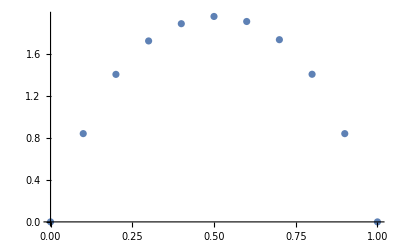

```mathematica
differences=Table[With[{degrees=VertexDegree[RandomGraph[BernoulliGraphDistribution[5, 1-m]]]},Max[degrees]-Min[degrees]],{m,0,1,0.1},{k,10000}  (*100 trials for each m*)];

averages=Mean/@differences;
Transpose[{Range[0,1,0.1],averages}];
ListPlot[%]
```

```mathematica
sparsities=Table[Module[{g,n,e,sparsity},g=RandomGraph[BernoulliGraphDistribution[5, 1-m]];
n=VertexCount[g];
e=EdgeCount[g];
sparsity=2 e/(n (n-1));
sparsity],{m,0,1,0.1},{k,100}  (*100 trials per m*)];

averageSparsities=Mean/@sparsities;
```

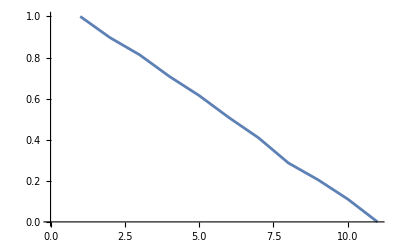

```mathematica
ListLinePlot[averageSparsities]
```

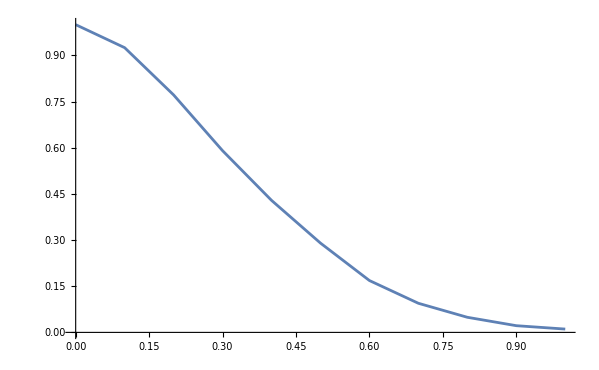

```mathematica
ListLinePlot[d]
```

```mathematica
k=1000
d=Table[N[Lookup[#,True,0]/(Lookup[#,True,0]+Lookup[#,False,0])]&@Counts[SimpleGraphQ/@Table[
configurationModel[VertexDegree[UndirectedGraph[IGBarabasiAlbertGame[m,2]]]]
,{k}
]],{m,1,15}]
```

1000

{1.,1.,0.524,0.164,0.05,0.015,0.012,0.001,0.003,0.001,0.,0.001,0.,0.001,0.}

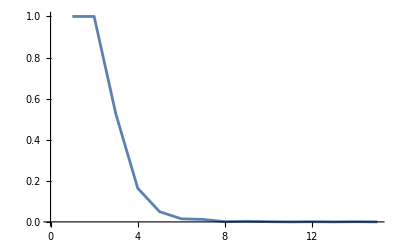

```mathematica
ListLinePlot[d]
```

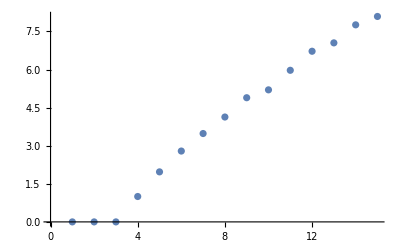

```mathematica
differences=Table[With[{degrees=VertexDegree[UndirectedGraph[IGBarabasiAlbertGame[m,2]]]},Max[degrees]-Min[degrees]],{m,1,15},{k,100}];

averages=Mean/@differences;
ListPlot[%]
```

```mathematica
d=Table[N[Lookup[#,True,0]/(Lookup[#,True,0]+Lookup[#,False,0])]&@Counts[SimpleGraphQ/@Table[
configurationModel[VertexDegree[UndirectedGraph[IGBarabasiAlbertGame[m,2]]]]
,{k}
]],{m,1,15}]
```

```mathematica
differences=Table[With[{degrees=VertexDegree[UndirectedGraph[IGBarabasiAlbertGame[m,2]]]},Max[degrees]-Min[degrees]],{m,1,15},{k,1000}];

averages=Mean/@differences;
```

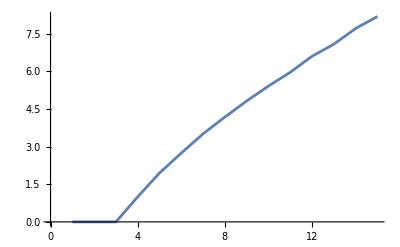

```mathematica
ListLinePlot[averages]
```

```mathematica
sparsities=Table[Module[{g,n,e,sparsity},g=UndirectedGraph[IGBarabasiAlbertGame[m,2]];
n=VertexCount[g];
e=EdgeCount[g];
sparsity=2 e/(n (n-1));
sparsity],{m,1,15},{k,100}  (*100 trials per m*)];

averageSparsities=Mean/@sparsities;
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

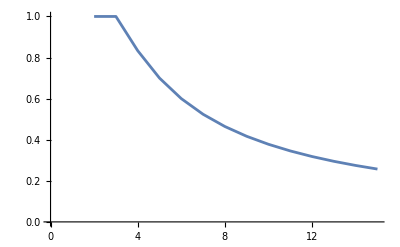

```mathematica
ListLinePlot[averageSparsities]
```

Sparsity and difference between min and max degree has a bad effect. Look at power-law distributed graphs such as Barabási Albert graphs.

```mathematica
Graph[#, ImageSize->40]&/@IGData[{"AllDirectedGraphs",3}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
IGMotifs[RandomGraph[BernoulliGraphDistribution[100, 0.3]], 3]
```

{Indeterminate,Indeterminate,31312,4535}

```mathematica
networks=ExampleData/@Select[ExampleData["NetworkGraph"], StringStartsQ["Metabolic"]@*Last];
```

```mathematica
networks[[1]]
```

-Graphics-

```mathematica
configurationModel[VertexDegree[networks[[1]]]]
```

-Graphics-

```mathematica
IGMotifs[networks[[3]],3]
```

{Indeterminate,Indeterminate,11714,Indeterminate,24689,385,12788,0,0,432,11,0,0,0,0,0}

```mathematica
g=networks[[1]];
IGRewire[g, Floor[Length@VertexDegree[networks[[1]]]/3]]
```

-Graphics-

```mathematica
a=Table[IGMotifs[networks[[k]],3]/
(Mean/@N@Transpose[Table[IGMotifs[IGRewire[networks[[k]], Floor[Length@VertexDegree[networks[[k]]]]*4],3],{20}]]),{k, 1,Length[networks]}];
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

```mathematica
a//Dataset
```

```mathematica
Mean/@Transpose[a]
```

{Indeterminate,Indeterminate,1.16105,Indeterminate,1.16071,0.272965,1.15549,0.,0.,0.286471,0.432183,0.,0.,0.,0.,Indeterminate}

```mathematica
StandardDeviation/@Transpose[a]
```

{Indeterminate,Indeterminate,0.0209998,Indeterminate,0.0231511,0.0634136,0.0229079,0.,0.,0.0735344,0.966891,0.,0.,0.,0.,Indeterminate}

```mathematica
Max/@Transpose[a]
```

{Indeterminate,Indeterminate,1.20307,Indeterminate,1.21213,0.405268,1.20126,0.,0.,0.445869,6.25592,0.,0.,0.,0.,Indeterminate}

```mathematica
Min/@Transpose[a]
```

{Indeterminate,Indeterminate,1.08852,Indeterminate,1.08742,0.122299,1.06574,0.,0.,0.133205,0.0408476,0.,0.,0.,0.,Indeterminate}

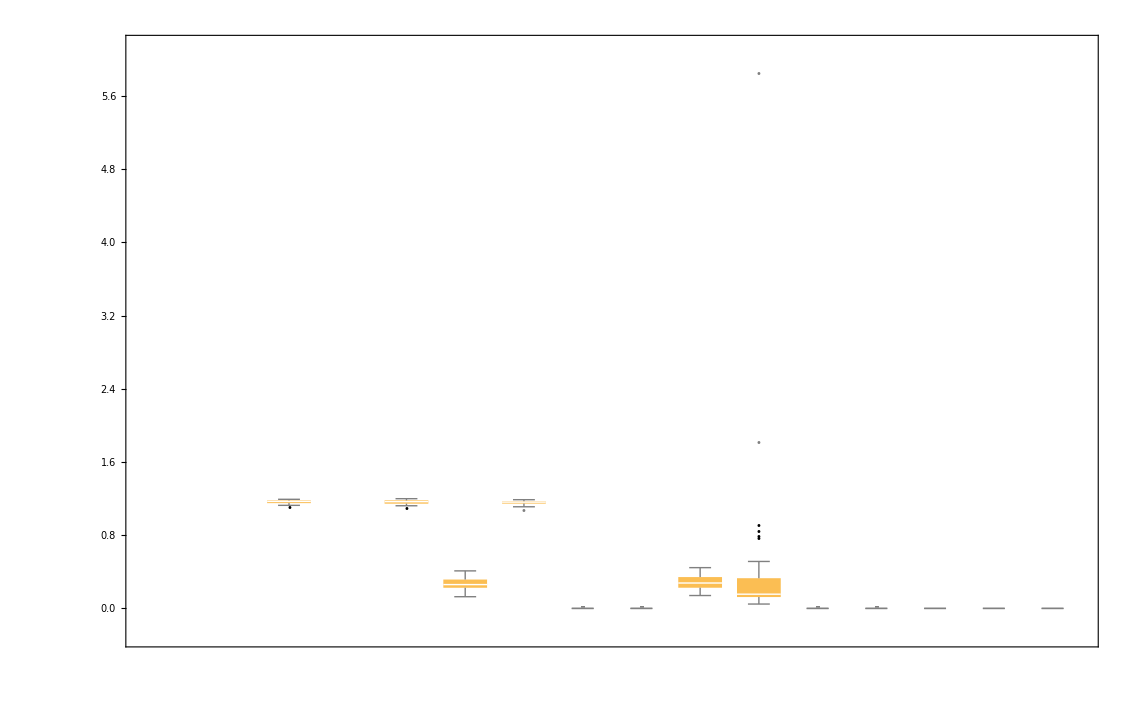

```mathematica
BoxWhiskerChart[Transpose[a],"Outliers",ChartLabels->(Graph[#]&)/@IGData[{"AllDirectedGraphs",3}],LabelingSize->40]
```

```mathematica
Length@VertexDegree[networks[[1]]]
```

993

```mathematica
k=10000;
```

```mathematica
d=Table[
Join[#,{n}]&/@Table[{m,N[Lookup[#,True,0]/(Lookup[#,True,0]+Lookup[#,False,0])]}&@Counts[SimpleGraphQ/@Table[
configurationModel[VertexDegree[RandomGraph[BernoulliGraphDistribution[n, m/Binomial[n, 2]]]]]
,{k}
]],{m,1, 10, 1}]
, {n, {10, 20, 30,40, 50, 60}}]
```

{{{1,0.9555,10},{2,0.8711,10},{3,0.7709,10},{4,0.6749,10},{5,0.5786,10},{6,0.4873,10},{7,0.4013,10},{8,0.3341,10},{9,0.2738,10},{10,0.218,10}},{{1,0.9798,20},{2,0.9357,20},{3,0.8799,20},{4,0.8323,20},{5,0.777,20},{6,0.7189,20},{7,0.6746,20},{8,0.6235,20},{9,0.5807,20},{10,0.5383,20}},{{1,0.9865,30},{2,0.9562,30},{3,0.9248,30},{4,0.8784,30},{5,0.8592,30},{6,0.8124,30},{7,0.7722,30},{8,0.7405,30},{9,0.708,30},{10,0.6729,30}},{{1,0.9889,40},{2,0.9666,40},{3,0.9389,40},{4,0.9097,40},{5,0.887,40},{6,0.8536,40},{7,0.8302,40},{8,0.8062,40},{9,0.7806,40},{10,0.7579,40}},{{1,0.9909,50},{2,0.9739,50},{3,0.9524,50},{4,0.9321,50},{5,0.9121,50},{6,0.8878,50},{7,0.8678,50},{8,0.8428,50},{9,0.8249,50},{10,0.8111,50}},{{1,0.9933,60},{2,0.9778,60},{3,0.9608,60},{4,0.9418,60},{5,0.9277,60},{6,0.9065,60},{7,0.8882,60},{8,0.8668,60},{9,0.843,60},{10,0.834,60}}}

{{1,0.9555,10},{2,0.8711,10},{3,0.7709,10},{4,0.6749,10},{5,0.5786,10},{6,0.4873,10},{7,0.4013,10},{8,0.3341,10},{9,0.2738,10},{10,0.218,10},{1,0.9798,20},{2,0.9357,20},{3,0.8799,20},{4,0.8323,20},{5,0.777,20},{6,0.7189,20},{7,0.6746,20},{8,0.6235,20},{9,0.5807,20},{10,0.5383,20},{1,0.9865,30},{2,0.9562,30},{3,0.9248,30},{4,0.8784,30},{5,0.8592,30},{6,0.8124,30},{7,0.7722,30},{8,0.7405,30},{9,0.708,30},{10,0.6729,30},{1,0.9889,40},{2,0.9666,40},{3,0.9389,40},{4,0.9097,40},{5,0.887,40},{6,0.8536,40},{7,0.8302,40},{8,0.8062,40},{9,0.7806,40},{10,0.7579,40},{1,0.9909,50},{2,0.9739,50},{3,0.9524,50},{4,0.9321,50},{5,0.9121,50},{6,0.8878,50},{7,0.8678,50},{8,0.8428,50},{9,0.8249,50},{10,0.8111,50},{1,0.9933,60},{2,0.9778,60},{3,0.9608,60},{4,0.9418,60},{5,0.9277,60},{6,0.9065,60},{7,0.8882,60},{8,0.8668,60},{9,0.843,60},{10,0.834,60}}

```mathematica
ListPlot3D[Flatten[d,1],AxesLabel->{"m","p","n"},Ticks->{Automatic,Automatic,Automatic},Boxed->True,AxesStyle->Directive[Black,Thick],Mesh->All]
```

-Graphics3D-

```mathematica
d=Table[{1-m,N[Lookup[#,True,0]/(Lookup[#,True,0]+Lookup[#,False,0])]}&@Counts[SimpleGraphQ/@Table[
configurationModel[VertexDegree[RandomGraph[BernoulliGraphDistribution[40, 1-m]]]]
,{k}
]],{m,0,1, 0.1}]
```

{{1.,0.},{0.9,0.},{0.8,0.},{0.7,0.},{0.6,0.},{0.5,0.},{0.4,0.},{0.3,0.},{0.2,0.},{0.1,0.009},{0.,1.}}

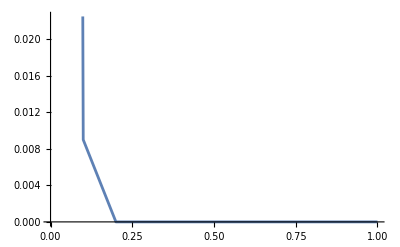

```mathematica
ListLinePlot[d]
```

```mathematica
n=10;
da=Table[{m,N[Lookup[#,True,0]/(Lookup[#,True,0]+Lookup[#,False,0])]}&@Counts[SimpleGraphQ/@Table[
configurationModel[VertexDegree[RandomGraph[BernoulliGraphDistribution[n, m/Binomial[n, 2]]]]]
,{k}
]],{m,1, 10, 1}]
```

{{1,0.962},{2,0.8752},{3,0.7859},{4,0.668},{5,0.59},{6,0.4874},{7,0.4079},{8,0.3386},{9,0.2707},{10,0.2233}}

```mathematica
ListLinePlot[da,AxesLabel->{"m","p"}]
```

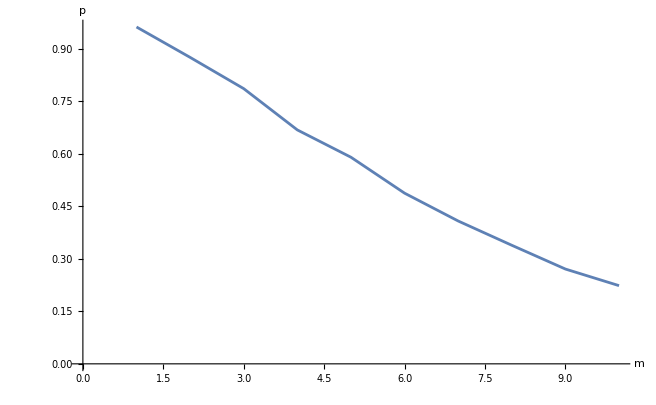

```mathematica
n=10;
da=Table[{n,N[Lookup[#,True,0]/(Lookup[#,True,0]+Lookup[#,False,0])]}&@Counts[SimpleGraphQ/@Table[
configurationModel[VertexDegree[RandomGraph[BernoulliGraphDistribution[n, 10/Binomial[n, 2]]]]]
,{k}
]],{n,10,60, 10}]
```

{{10,0.2129},{20,0.5255},{30,0.6783},{40,0.745},{50,0.7989},{60,0.8357}}

```mathematica
ListLinePlot[da,AxesLabel->{"n","p"}]
```

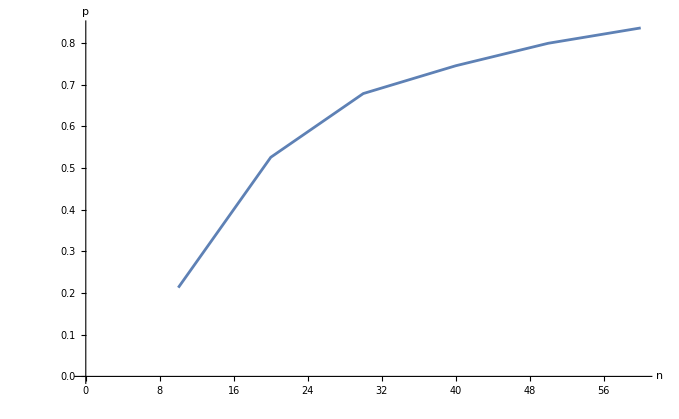

```mathematica
Table[{n,Mean@@@#}&/@Table[Module[{g,v,e,sparsity},
g=RandomGraph[BernoulliGraphDistribution[n, 10/Binomial[n,2]]];
v=VertexCount[g];
e=EdgeCount[g];
sparsity=2 e/(v (v-1));
sparsity
],{1000} ],{n,10,60, 3}];

averageSparsities=Mean/@%
d=N[%]
```

{{10,493/2250},{13,503/3900},{16,9971/120000},{19,1973/34200},{22,1997/46200},{25,1243/37500},{28,10163/378000},{31,327/15500},{34,571/33000},{37,2021/133200},{40,9923/780000},{43,4969/451500},{46,833/86250},{49,9943/1176000},{52,379/51000},{55,248/37125},{58,3357/551000}}

{{10.,0.219111},{13.,0.128974},{16.,0.0830917},{19.,0.0576901},{22.,0.0432251},{25.,0.0331467},{28.,0.0268862},{31.,0.0210968},{34.,0.017303},{37.,0.0151727},{40.,0.0127218},{43.,0.0110055},{46.,0.00965797},{49.,0.00845493},{52.,0.00743137},{55.,0.00668013},{58.,0.00609256}}

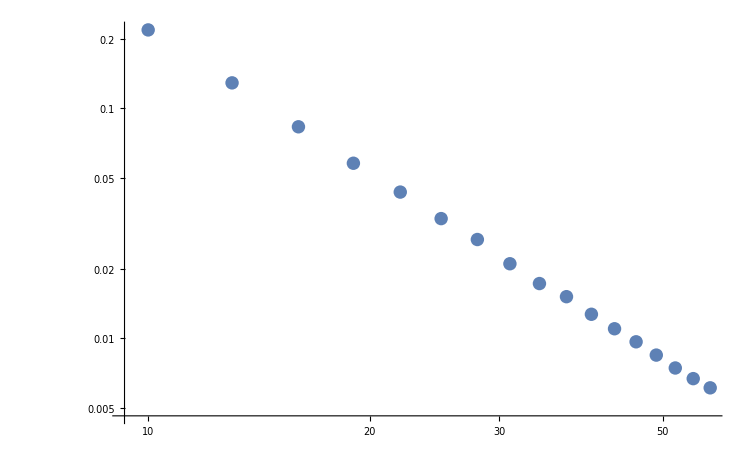

```mathematica
ListLogLogPlot[d]
```

```mathematica
Table[{m,Mean@@@#}&/@Table[Module[{g,v,e,sparsity},
g=RandomGraph[BernoulliGraphDistribution[50, m/Binomial[50,2]]];
v=VertexCount[g];
e=EdgeCount[g];
sparsity=2 e/(v (v-1));
sparsity
],{1000} ],{m,10,60, 3}];

averageSparsities=Mean/@%
db=N[%]
```

{{10,407/49000},{13,2591/245000},{16,3167/245000},{19,9501/612500},{22,3147/175000},{25,24531/1225000},{28,28351/1225000},{31,223/8750},{34,8437/306250},{37,18483/612500},{40,20031/612500},{43,1079/30625},{46,11531/306250},{49,4917/122500},{52,5207/122500},{55,563/12500},{58,57851/1225000}}

{{10.,0.00830612},{13.,0.0105755},{16.,0.0129265},{19.,0.0155118},{22.,0.0179829},{25.,0.0200253},{28.,0.0231437},{31.,0.0254857},{34.,0.0275494},{37.,0.0301763},{40.,0.0327037},{43.,0.0352327},{46.,0.0376522},{49.,0.0401388},{52.,0.0425061},{55.,0.04504},{58.,0.0472253}}

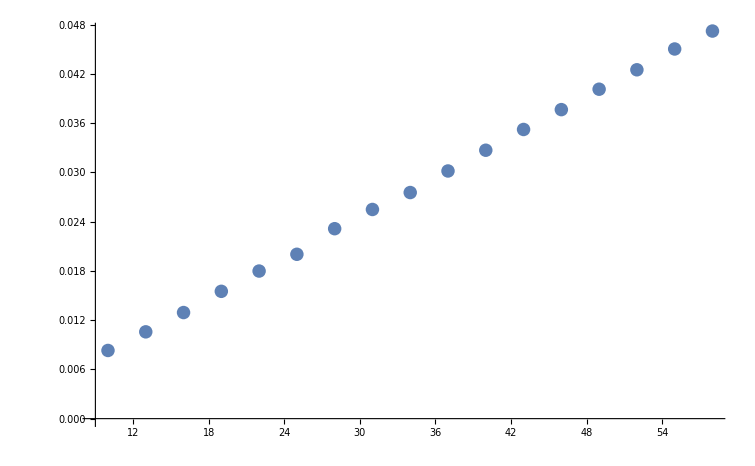

```mathematica
ListPlot[db]
```

```mathematica
Table[{m,Mean@@@#}&/@Table[Module[{g,v,e,sparsity},
g=StarGraph[m];
v=VertexCount[g];
e=EdgeCount[g];
sparsity=2 e/(v (v-1));
sparsity
],{1000} ],{m,10,60, 3}]
```

```mathematica
m=10;
g=Null;
While[!SimpleGraphQ[g],g=configurationModel[Prepend[ConstantArray[1,m],m]]];
g
```

$Aborted

configurationModel[{10,1,1,1,1,1,1,1,1,1,1}]

```mathematica
Table[{n,Mean@@@#}&/@Table[Module[{g,v,e,sparsity},
g=StarGraph[n];
v=VertexCount[g];
e=EdgeCount[g];
sparsity=2 e/(v (v-1));
sparsity
],{1000} ],{n,10,60, 3}];

averageSparsities=Mean/@%
d=N[%]
```

{{10,1/5},{13,2/13},{16,1/8},{19,2/19},{22,1/11},{25,2/25},{28,1/14},{31,2/31},{34,1/17},{37,2/37},{40,1/20},{43,2/43},{46,1/23},{49,2/49},{52,1/26},{55,2/55},{58,1/29}}

{{10.,0.2},{13.,0.153846},{16.,0.125},{19.,0.105263},{22.,0.0909091},{25.,0.08},{28.,0.0714286},{31.,0.0645161},{34.,0.0588235},{37.,0.0540541},{40.,0.05},{43.,0.0465116},{46.,0.0434783},{49.,0.0408163},{52.,0.0384615},{55.,0.0363636},{58.,0.0344828}}

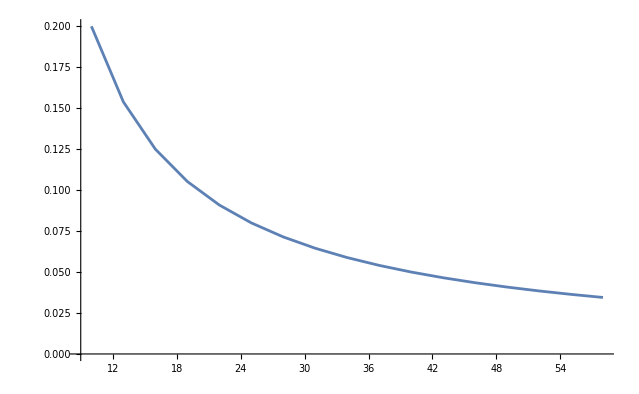

```mathematica
ListLinePlot[d]
```

```mathematica
k=10000;
d=Table[N[Lookup[#,True,0]/(Lookup[#,True,0]+Lookup[#,False,0])]&@Counts[SimpleGraphQ/@Table[
configurationModel[VertexDegree[StarGraph[m]]]
,{k}
]],{m,1,15}]
```

{1.,1.,0.6702,0.3969,0.2285,0.1234,0.0639,0.0374,0.0197,0.0105,0.0053,0.0031,0.0007,0.0007,0.0004}

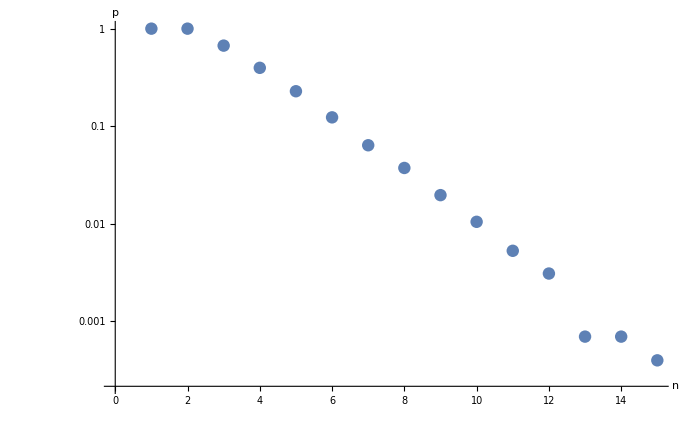

```mathematica
ListLogPlot[d,AxesLabel->{"n","p"}]
```

```mathematica
Variance[VertexDegree[RandomGraph[BernoulliGraphDistribution[10,7/Binomial[10,2]]]]]
```

16/15

```mathematica
Mean/@Table[{n,#}&/@Table[Module[{g,v,e,sparsity},
g=StarGraph[n];
Variance[VertexDegree[g]]
],{1000} ],{n,10,60, 3}];

d=N[%]
```

{{10.,6.4},{13.,9.30769},{16.,12.25},{19.,15.2105},{22.,18.1818},{25.,21.16},{28.,24.1429},{31.,27.129},{34.,30.1176},{37.,33.1081},{40.,36.1},{43.,39.093},{46.,42.087},{49.,45.0816},{52.,48.0769},{55.,51.0727},{58.,54.069}}

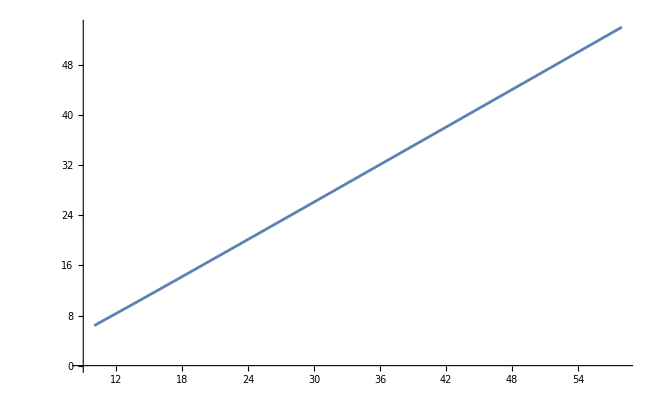

```mathematica
ListLinePlot[d]
```

```mathematica
Mean/@Table[{m,#}&/@Table[Module[{g,v,e,sparsity},
g=RandomGraph[BernoulliGraphDistribution[50, m/Binomial[50,2]]];
Variance[VertexDegree[g]]
],{1000} ],{m,10,60, 3}];

d=N[%]
```

{{10.,0.39122},{13.,0.501711},{16.,0.615479},{19.,0.724841},{22.,0.849347},{25.,0.962519},{28.,1.05518},{31.,1.18388},{34.,1.29263},{37.,1.40278},{40.,1.5044},{43.,1.64771},{46.,1.72056},{49.,1.84424},{52.,1.97319},{55.,2.07137},{58.,2.14278}}

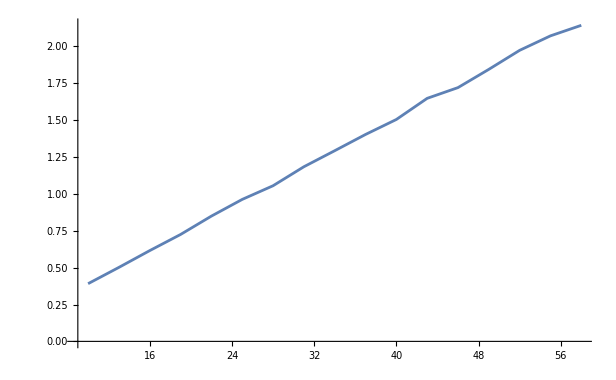

```mathematica
ListLinePlot[d]
```

```mathematica
Mean/@Table[{n,#}&/@Table[Module[{g,v,e,sparsity},
g=RandomGraph[BernoulliGraphDistribution[n, 10/Binomial[n,2]]];
Variance[VertexDegree[g]]
],{1000} ],{n,10,60, 3}];

d=N[%]
```

{{10.,1.34787},{13.,1.20603},{16.,1.10188},{19.,0.921175},{22.,0.833281},{25.,0.752337},{28.,0.684376},{31.,0.618204},{34.,0.558093},{37.,0.521722},{40.,0.477046},{43.,0.453773},{46.,0.416614},{49.,0.391827},{52.,0.372235},{55.,0.359987},{58.,0.341739}}

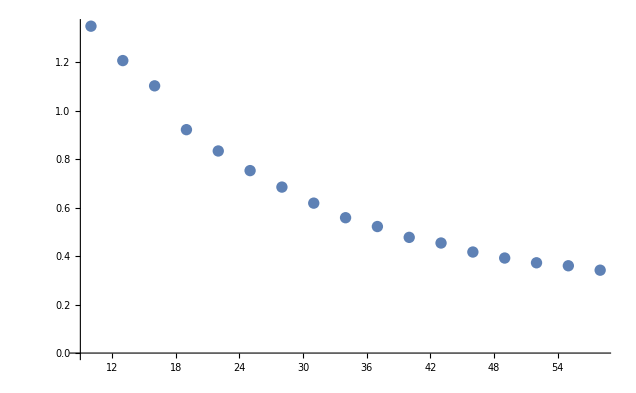

```mathematica
ListPlot[d]
```

```mathematica
d=Table[N[Lookup[#,True,0]/(Lookup[#,True,0]+Lookup[#,False,0])]&@Counts[SimpleGraphQ/@Table[
configurationModel[VertexDegree[UndirectedGraph[IGBarabasiAlbertGame[m,2]]]]
,{1000}
]],{m,1,15}]
```

{1.,1.,0.548,0.162,0.052,0.021,0.008,0.008,0.004,0.002,0.001,0.,0.001,0.001,0.}

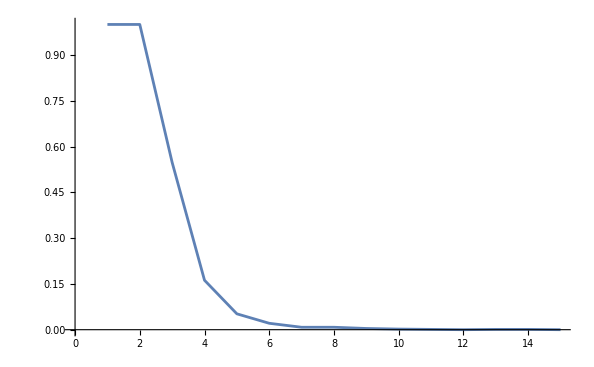

```mathematica
ListLinePlot[d]
```

```mathematica
Table[{n,Mean@@@#}&/@Table[Module[{g,v,e,sparsity},
g=UndirectedGraph[IGBarabasiAlbertGame[n,2]];
v=VertexCount[g];
e=EdgeCount[g];
sparsity=2 e/(v (v-1));
sparsity
],{1000} ],{n,10,60, 3}];

averageSparsities=Mean/@%
d=N[%]
```

{{10,17/45},{13,23/78},{16,29/120},{19,35/171},{22,41/231},{25,47/300},{28,53/378},{31,59/465},{34,65/561},{37,71/666},{40,77/780},{43,83/903},{46,89/1035},{49,95/1176},{52,101/1326},{55,107/1485},{58,113/1653}}

{{10.,0.377778},{13.,0.294872},{16.,0.241667},{19.,0.204678},{22.,0.177489},{25.,0.156667},{28.,0.140212},{31.,0.126882},{34.,0.115865},{37.,0.106607},{40.,0.0987179},{43.,0.0919158},{46.,0.0859903},{49.,0.0807823},{52.,0.0761689},{55.,0.0720539},{58.,0.0683606}}

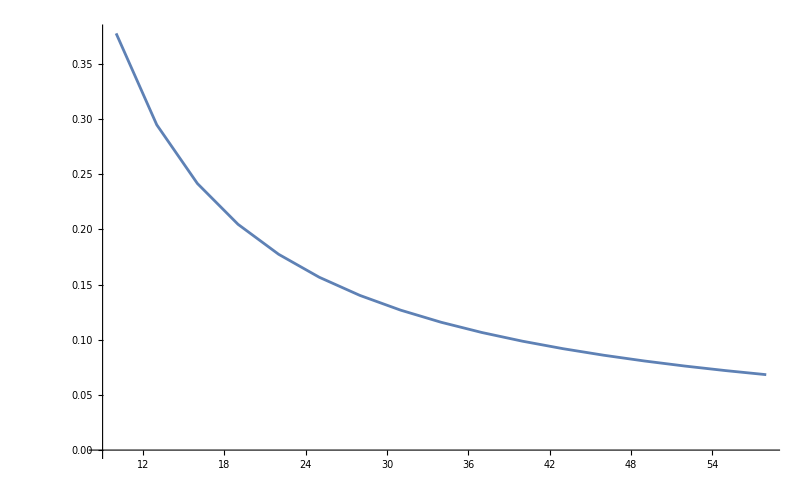

```mathematica
ListLinePlot[d]
```

```mathematica
Mean/@Table[{n,#}&/@Table[Module[{g,v,e,sparsity},
g=UndirectedGraph[IGBarabasiAlbertGame[n,2]];
Variance[VertexDegree[g]]
],{1000} ],{n,10,60, 3}];

d=N[%]
```

{{10.,4.032},{13.,5.75373},{16.,7.25467},{19.,8.70696},{22.,9.89408},{25.,11.2357},{28.,12.0865},{31.,12.7631},{34.,13.9469},{37.,14.965},{40.,15.7834},{43.,16.4471},{46.,17.6415},{49.,18.1297},{52.,18.9129},{55.,19.553},{58.,19.948}}

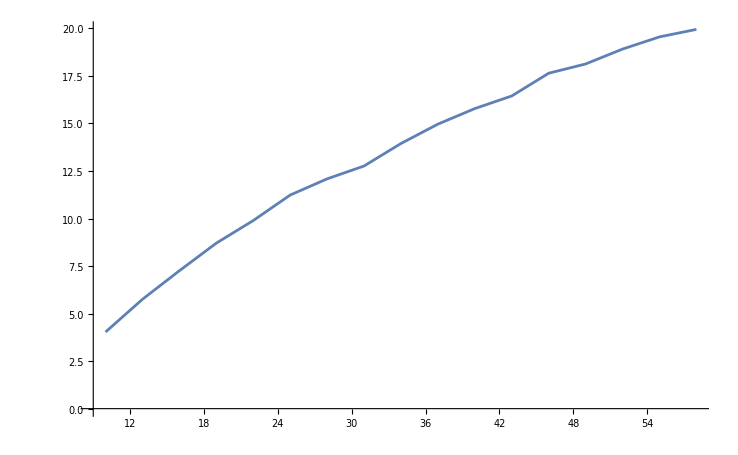

```mathematica
ListLinePlot[d]
```

```mathematica
differences=Table[With[{degrees=VertexDegree[UndirectedGraph[IGBarabasiAlbertGame[m,2]]]},Max[degrees]-Min[degrees]],{m,1,15},{k,1000}];

averages=Mean/@differences;
```

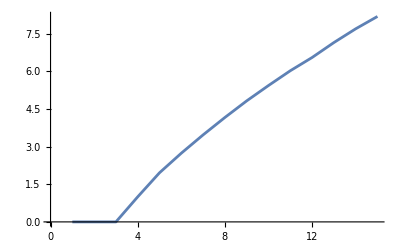

```mathematica
ListLinePlot[averages]
```